# Single infection with trophical transmission

## Ecological dynamics of a resident

```mathematica
dIsdt = R[Iw, Is]- d Is- Π0[Ds, Dw] Is  - γw W Is ;(*Susceptible intermediate*)
dIwdt =  γw W Is  - (d + α)Iw - Π1[Ds, Dw, βw]Iw; (*Infected intermediate*)
dDsdt =B[Ds, Dw, Is, Iw]  - μ Ds - λ[βw, Iw] Ds;  (*Susceptible definitive*)
dDwdt =λ[βw, Iw] Ds- (μ + σ) Dw ;(*Infected definitive*)
dWdt = fw Dw - δ W - γw W Is;
```

```mathematica
func0 = {R[Iw, Is] -> r(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
func1 =  {R[Iw, Is] -> r(1- (Is + Iw)/Κ)(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
var = {Is, Iw, Ds, Dw, W};
vart = {Is[t], Iw[t], Ds[t], Dw[t], W[t]};
sys = {dIsdt, dIwdt, dDsdt, dDwdt, dWdt};
```

```mathematica
solW0 = Solve[Thread[sys == 0]/.func0/.W-> 0,{Is, Iw, Ds, Dw}]
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-d+r)/ρ,Dw→0}}

```mathematica
solW0Func1= Solve[Thread[sys == 0]/.func1/.W-> 0,{Is, Iw, Ds, Dw}]//FullSimplify
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→Κ-(d Κ)/r,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-r μ+c (-d+r) Κ ρ)/(c Κ ρ^2),Dw→0}}

Stability of the equilibrium

## Linear functions

```mathematica
A = {{r - d - Π0[Ds, Dw] - γw W, r, 0, 0, 0}, {γw W, - (d + α)-  Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
A//MatrixForm
```

(-d+r-W γw-Π0[Ds,Dw] | r | 0 | 0 | 0
W γw | -d-α-Π1[Ds,Dw,βw] | 0 | 0 | 0
0 | 0 | -Iw βw-μ+c (Is+Iw) ρ | c (Is+Iw) ρ | 0
0 | 0 | Iw βw | -μ-σ | 0
0 | 0 | 0 | fw | -Is γw-δ)

```mathematica
(A.var /.func0)== (sys/.func0)//FullSimplify
```

True

```mathematica
Aeigens = Eigenvalues[A/.func0]//FullSimplify;
```

```mathematica
FullSimplify[Aeigens/.solW0[[1]]/.W-> 0, Assumptions->{α>0, r>0, σ>0}]
```

{-δ,-d-α,-d+r,-μ-σ,-μ}

```mathematica
FullSimplify[Aeigens/.solW0[[2]]/.W-> 0, Assumptions->{r>0, d>0,μ>0, σ>0, ρ>0, α>0, βw>0}]
```

{-δ-(γw μ)/(c ρ),-(-d βw+r βw+(r+α) ρ+Abs[-d βw+r βw+(r+α) ρ])/(2 ρ),Piecewise[{{(d βw-α ρ-r (βw+ρ))/ρ, d βw>α ρ+r (βw+ρ)}, {0, True}}],-μ-σ,0}

## Logistic growth intermediate hosts

```mathematica
AFunc1 = {{r(1-(Is + Iw)/Κ) - d - Π0[Ds, Dw]-  γw W, r(1-(Is + Iw)/Κ), 0, 0, 0}, {γw W, - (d + α)- Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
(AFunc1/.func1).var == (sys/.func1)//FullSimplify
```

True

```mathematica
AeigensFunc1 = Eigenvalues[AFunc1/.func1]//FullSimplify
```

{-Is γw-δ,-1/(2 Κ)(Is r+Iw r+√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),-1/(2 Κ)(Is r+Iw r-√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ-√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2)),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ+√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2))}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[2]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d, (c p (-d+r) Κ+r σ)>0}]
```

{-δ+((d-r) γw Κ)/r,-d-α,0,-(c p (d-r) Κ+r (2 μ+σ)+Abs[c p (-d+r) Κ+r σ])/(2 r),(c p (-d+r) Κ-r (2 μ+σ)+Abs[c p (-d+r) Κ+r σ])/(2 r)}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[3]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d,  c> 0, μ+σ>0, p>0}]
```

{-δ-(γw μ)/(c p),-(c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ+√((c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ)^2))/(2 c p^2 Κ),(-c p (p (r+α)+(-d+r) βw) Κ+r (p+βw) μ+√((c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ)^2))/(2 c p^2 Κ),-μ-σ,0}

```mathematica
makeSystem[var_, vart_, sys_]:= (syst = sys/.Thread[var-> vart]; sysfull = Thread[D[vart, t] == syst]);
```

Numerical analysis

```mathematica
sysFunc0 = makeSystem[var,vart ,  sys/.func0];
sysFunc1 = makeSystem[var,vart ,  sys/.func1];
```

```mathematica
prEco = {r -> 1.5, d -> 1.1, ρ -> 1.2,γw -> 4.5, α-> 0, βw-> 2.5, c-> 0.4, μ-> 1.9, σ-> 0, fw -> 14.5, δ-> 1.9};
```

```mathematica
maxt = 100;
initFunc0= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 30 };
NSolve[Thread[(sys/.func0/.prEco) == 0], var];
ndsol0Func0 = NDSolve[Join[sysFunc0/.prEco, initFunc0], var, {t, 0, maxt}]
```

NDSolve::ndsz: At t == 55.1567, step size is effectively zero; singularity or stiff system suspected.

{{Is→InterpolatingFunction[{{0., 55.1567}}, <>],Iw→InterpolatingFunction[{{0., 55.1567}}, <>],Ds→InterpolatingFunction[{{0., 55.1567}}, <>],Dw→InterpolatingFunction[{{0., 55.1567}}, <>],W→InterpolatingFunction[{{0., 55.1567}}, <>]}}

```mathematica
Plot[Evaluate[vart/.ndsol0Func0], {t, 0, maxt}, PlotRange->All, PlotLegends->{"Is", "Iw", "Ds", "Dw", "W"}]
```

-Graphics-

```mathematica
prEcoFunc1 = {r -> 4.5, d -> 1.1, ρ-> 0.5,γw -> 5.5, α-> 0, βw-> 1.5, c-> 0.4, μ-> 0.9, σ-> 0, fw -> 14.5, δ-> 9.9, Κ-> 50};
maxt = 700;
initFunc1= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 100 };
NSolve[Thread[(sys/.func1/.prEcoFunc1) == 0], var]
ndsol0Func1 = NDSolve[Join[sysFunc1/.prEcoFunc1, initFunc1], var, {t, 0, maxt}]
```

{{Is→-1.8,Iw→39.5778,Ds→0.,Dw→0.,W→-4.39753},{Is→37.7778,Iw→0.,Ds→0.,Dw→0.,W→0.},{Is→38.3778,Iw→-0.6,Ds→0.0476521,Dw→-0.0476521,W→-0.00312681},{Is→-3.71631,Iw→8.21631,Ds→0.0629334,Dw→0.8618,W→-1.18562},{Is→2.01854,Iw→2.48146,Ds→0.439411,Dw→1.8173,W→1.25468},{Is→4.5,Iw→0.,Ds→5.99,Dw→0.,W→0.},{Is→0.6,Iw→-0.6,Ds→0.182069,Dw→-0.182069,W→-0.2},{Is→-1.8,Iw→1.8,Ds→0.,Dw→0.,W→-0.2},{Is→27.3341,Iw→-22.8341,Ds→0.0113651,Dw→-0.432521,W→-0.0391391},{Is→0.,Iw→0.,Ds→0.,Dw→0.,W→0.}}

{{Is→InterpolatingFunction[{{0., 700.}}, <>],Iw→InterpolatingFunction[{{0., 700.}}, <>],Ds→InterpolatingFunction[{{0., 700.}}, <>],Dw→InterpolatingFunction[{{0., 700.}}, <>],W→InterpolatingFunction[{{0., 700.}}, <>]}}

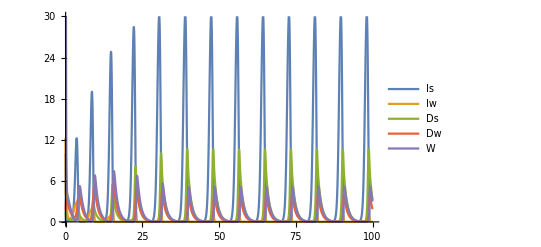

```mathematica
Plot[Evaluate[vart/.ndsol0Func1], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 30}}, PlotLegends->{"Is", "Iw", "Ds","Dw", "W"}]
```

## Mutant dynamics

```mathematica
dImudt = γm M Is  - (d + α)Imu -(Ds+Dw) (ρ+βm)Imu; (*Infected intermediate*)
dDmdt = Imu βm Ds - (μ + σ)Dm;
dMdt = fm Dm - δ M - γm Is M;
```

```mathematica
dMdt > 0
```

```mathematica
Am = {{-d-α - (Ds+Dw) (ρ+βm), 0, γm Is},{βm Ds, -μ -σ, 0},{0, fm, -δ- γm Is}};
Am//MatrixForm
```

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
Am.{Imu, Dm, M} == {dImudt, dDmdt, dMdt}//FullSimplify
```

True

```mathematica
FMat = {{0, 0, 0},{0, 0, 0}, {0, fm, 0}};
```

```mathematica
VMat ={{d+α+(Ds+Dw) (ρ+βm), 0, - Is γm},{-Ds βm, μ + σ, 0}, {0, 0, Is γm + δ}};
```

```mathematica
FMat - VMat == Am//FullSimplify
FMat-VMat//MatrixForm
```

True

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
R0 = Eigenvalues[FMat.Inverse[VMat]][[3]]//FullSimplify
```

(Ds fm Is βm γm)/((Is γm+δ) (d+α+(Ds+Dw) (βm+ρ)) (μ+σ))

R0=fm/(Is γm+δ)(Is  γm)/(d+α+(Ds+Dw) (ρ+βm))(Ds  βm)/(μ+σ)

# Double infection

## Resident and mutant dynamics

Assumptions:
1. Fixed number of total intermediate hosts and definitive hosts
2. An infinite parasite pool such that reproduction of parasite does not affect the dynamics of the pool
3. We track the frequency dynamics of four compartments instead of density dynamics: Iw: intermediate host infected with a wild type, Iww: intermediate host infected with two wild types, Dw: definitive host infected with a wild type, Dww: definitive host infected with two wild type.
Is: frequency of susceptible intermediate host (1 - Iw - Iww)
Ds: frequency of susceptible definitive host (1 - Dw - Dww)
p: probability that two parasites make it into the intermediate host
q: probability that two parasites make it into the definitive host

```mathematica
dIwdt =  (1-p)γ (1-m) Is - (d + αw)Iw -Π[βw] Iw; (*Infected intermediate*)
dIwwdt = p γ (1-m)^2 Is  - (d + αww)Iww -Π[βww] Iww;
dDwdt =λS Ds- (μ + σw) Dw -(λS + λSM + λmix)Dw;(*Infected definitive*)
dDwwdt = λC Ds + λS Dw + 1/2 λmix Dw - (μ + σww)Dww;
```

```mathematica
dImdt = (1-p)γ m Is  - (d + αm)Imut - Π[βm]Imut;
dImwdt =2 p γ m(1-m)Is   - (d + αwm) Imw - Π[βmw] Imw;
dImmdt = p γ  m^2 Is  - (d + αmm)Imm - Π[βmm]Imm;
dDmdt = λSM Ds - (μ + σm)Dw - (λSM + λS + λmix)Dm;
dDmwdt = λCMW Ds + (λS +1/2 λmix)Dm + (λSM + 1/2λmix) Dw+(1-q)βmw Imw Dm - (μ + σmw) Dmw;
dDmmdt = λCMDs +(λSM+1/2λmix) Dm - (μ + σmm) Dmm;
```

```mathematica
condFixTotal = {Is -> (1 - Iw - Iww), Ds -> (1 - Dw - Dww)};
Π[x_] := (b0 +x);
λS= (βw Iw + (1-q)βww Iww);
λC = q βww Iww;
λSM = βm Imut + (1-q)βmw Imw + (1-q)βmm Imm;
λmix =  q βmw Imw;
λCM = q βmm Imm;
```

## Analysing the resident dynamics

Equilibrium

```mathematica
condResOnly = {m-> 0,Imut-> 0,  Imm-> 0, Imw -> 0};
```

```mathematica
solsres = Solve[{dIwdt == 0, dIwwdt == 0, dDwdt == 0, dDwwdt == 0}/.condFixTotal/.condResOnly, {Iw, Iww, Dw, Dww}];
```

```mathematica
Iw/.solsres;
Reduce[%>0 && γ > 0 && b0 > 0 && d > 0 && αww >0 && βww > 0 && 0≤ p≤1 && αw > 0 , Reals]
```

βww>0&&αww>0&&d>0&&b0>0&&0≤p<1&&γ>0&&αw>0&&βw>1/(b0+d+αww+βww+p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βww-d βww-αw βww-b0 γ-d γ-p αw γ-αww γ+p αww γ-βww γ+p βww γ)

```mathematica
1/(b0+d+αww+βww+p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βww-d βww-αw βww-b0 γ-d γ-p αw γ-αww γ+p αww γ-βww γ+p βww γ)//FullSimplify
```

-((b0+d+αw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww-βww)+βww) γ)/(b0+d+αww+βww+p γ)

-((b0+d+αw) (b0+d+αww+βww)+(b0+d+αww+βww)γ+p (αw-αww-βww) γ)/(b0+d+αww+βww+p γ)
-((b0+d+αw) (b0+d+αww+βww)+(b0+d+αww+βww)γ+p (αw-αww-βww) γ)/(b0+d+αww+βww+p γ)
-((b0+d+αw + γ) (b0+d+αww+βww)+p (αw-αww-βww) γ)/(b0+d+αww+βww+p γ)
-((b0+d+αw ) (b0+d+αww+βww)+ γ (b0+d)+p  γ αw + γ(αww+βww)(1-p))/(b0+d+αww+βww+p γ)

```mathematica
-((b0+d+αw ) (b0+d+αww+βww)+ γ (b0+d)+p  γ αw + γ(αww+βww)(1-p))/(b0+d+αww+βww+p γ)== 1/(b0+d+αww+βww+p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βww-d βww-αw βww-b0 γ-d γ-p αw γ-αww γ+p αww γ-βww γ+p βww γ)//FullSimplify
```

```mathematica
Iww/.solsres;
Reduce[% > 0 && αw > 0 && 0≤ p ≤ 1 && βw > 0 && d > 0 && b0 > 0 && γ > 0 && αww > 0 , βww,Reals]
```

βw>0&&αw>0&&d>0&&b0>0&&0<p≤1&&γ>0&&αww>0&&βww>1/(b0+d+αw+βw+γ-p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βw-d βw-αww βw-b0 γ-d γ-p αw γ-αww γ+p αww γ-p βw γ)

```mathematica
1/(b0+d+αw+βw+γ-p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βw-d βw-αww βw-b0 γ-d γ-p αw γ-αww γ+p αww γ-p βw γ)//FullSimplify
```

-((b0+d+αww) (b0+d+αw+βw)+(b0+d+αww+p (αw-αww+βw)) γ)/(b0+d+αw+βw+γ-p γ)

-((b0+d+αww) (b0+d+αw+βw)+(b0+d+αww+p (αw-αww+βw)) γ)/(b0+d+αw+βw+γ-p γ)
-((b0+d+αww) (b0+d+αw+βw + γ)+p (αw-αww+βw)γ)/(b0+d+αw+βw+γ(1-p))
-((b0+d+αww) (b0+d+αw+βw) + γ(b0+d)+(αw+βw)p γ+ αww γ(1- p ))/(b0+d+αw+βw+γ(1-p))

```mathematica
Solve[{dDwdt == 0, dDwwdt == 0}/.condFixTotal/.condResOnly, {Dw, Dww}]
```

Equilibrium stability conditions

```mathematica
JRes = D[{dIwdt, dIwwdt, dDwdt, dDwwdt}/.condFixTotal/.condResOnly, {{Iw, Iww, Dw, Dww}}]//Simplify
```

{{-b0-d-αw-βw-γ+p γ,(-1+p) γ,0,0},{-p γ,-b0-d-αww-βww-p γ,0,0},{-(-1+2 Dw+Dww) βw,(-1+2 Dw+Dww) (-1+q) βww,-2 Iw βw+2 Iww (-1+q) βww-μ-σw,-Iw βw+Iww (-1+q) βww},{Dw βw,(Dw+q-2 Dw q-Dww q) βww,Iw βw+Iww (1-2 q) βww,-Iww q βww-μ-σww}}

```mathematica
JRes//MatrixForm
```

(-b0-d-αw-βw-γ+p γ | (-1+p) γ | 0 | 0
-p γ | -b0-d-αww-βww-p γ | 0 | 0
-(-1+2 Dw+Dww) βw | (-1+2 Dw+Dww) (-1+q) βww | -2 Iw βw+2 Iww (-1+q) βww-μ-σw | -Iw βw+Iww (-1+q) βww
Dw βw | (Dw+q-2 Dw q-Dww q) βww | Iw βw+Iww (1-2 q) βww | -Iww q βww-μ-σww)

```mathematica
eigvals = Eigenvalues[JRes]//FullSimplify;
```

Check with function Reduce

```mathematica
Reduce[eigvals[[2]]<0&& 1>p>0&& d > 0&&βw>0&&βww >0 && αw > 0&& αww > 0&& b0 > 0&& γ >0]
```

Check with some algebra

```mathematica
eigvals[[2]]
```

1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+√((αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2))

1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+√((αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2))
If p = 0:
(αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww)^2+2  (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww + γ)^2

The whole expression become
1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+|αw-αww+βw-βww + γ|) < 0 in all cases

If p = 1:
(αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww)^2-2  (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww - γ)^2
The whole expression become
1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+|αw-αww+βw-βww - γ|) < 0 in all cases

The eigenvalue cannot be imaginary because the part under the square root is always positive

```mathematica
Reduce[(αw-αww+βw-βww + γ)^2-4 p(αw-αww+βw-βww) γ < 0 && αww >0 && αw > 0&& βw > 0 && βww > 0 && 0<p<1 && γ > 0]
```

False

```mathematica
eigvals[[4]]
```

1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)

Check with function Reduce [Still there are some doubts]

```mathematica
Reduce[eigvals[[4]]>0&& 1>q>0&& d > 0&&βw>0&&βww >0 && σw > 0&& σww > 0&& Iww > 0&& Iw >0 && μ > 0]
```

False

Check with some algebra

If q = 0

1/2 (-2 Iw βw-2 Iww βww-2 μ-σw+√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))-σww)

1/2 (-2 Iw βw-2 Iww βww-2 μ-σw+√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))-σww)<0
iff 
2 Iw βw+2 Iww βww+2 μ+σw+σww>√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))
iff
(2 Iw βw+2 Iww βww+2 μ+σw+σww)^2>(σw-σww) (4 Iw βw+4 Iww βww+σw-σww)
iff
4 (Iw^2 βw^2+Iww^2 βww^2+2 Iww βww (μ+σww)+(μ+σw) (μ+σww)+2 Iw βw (Iww βww+μ+σww))) > 0  in all cases

Using some functions to simplify some expression above

```mathematica
Expand[(2 Iw βw+2 Iww βww+2 μ+σw+σww)^2]-Expand[(σw-σww) (4 Iw βw+4 Iww βww+σw-σww)]//FullSimplify
```

4 (Iw^2 βw^2+Iww^2 βww^2+2 Iww βww (μ+σww)+(μ+σw) (μ+σww)+2 Iw βw (Iww βww+μ+σww))

```mathematica
1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)/.q-> 0//FullSimplify
```

1/2 (-2 Iw βw-2 Iww βww-2 μ-σw+√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))-σww)

If q = 1
1/2 (-2 Iw βw-Iww βww-2 μ-σw-σww+√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2))

1/2 (-2 Iw βw-Iww βww-2 μ-σw-σww+√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2))< 0
iff 
2 Iw βw+Iww βww+2 μ+σw+σww>√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2)
iff
(2 Iw βw+Iww βww+2 μ+σw+σww)^2>4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2
iff
4 (Iw^2 βw^2+(μ+σw) (Iww βww+μ+σww)+Iw βw (Iww βww+2 (μ+σww)))>0 True in all cases

```mathematica
1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)/.q-> 1//FullSimplify
```

1/2 (-2 Iw βw-Iww βww-2 μ-σw-σww+√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2))

```mathematica
Expand[(2 Iw βw+Iww βww+2 μ+σw+σww)^2]-4 Iw βw (σw-σww)-Expand[(Iww βww-σw+σww)^2]//Simplify
```

4 (Iw^2 βw^2+(μ+σw) (Iww βww+μ+σww)+Iw βw (Iww βww+2 (μ+σww)))

Check if the part under the square root is negative (i.e. potential for imaginary eigenvalue)

```mathematica
ToExpression[Import["/Users/Linh-phuong/resstability.txt"]]
```

```mathematica
(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))/.Iw -> FullSimplify[Iw/.solsres]/.Iww -> FullSimplify[Iww/.solsres]//FullSimplify
AbsoluteTiming[Reduce[%>0 &&1>p>0 && 1>q>0&& d > 0&&βw>0&&βww >0 && σw > 0&& σww > 0&& αww > 0&& αw >0&&γ > 0 && b0 > 0]//Simplify]
```

{9454.62144,b0>0&&d>0&&αw>0&&αww>0&&βw>0&&βww>0&&((0<p≤(βw (b0+d+αww+βww))/(αww βw+αw βww+2 βw βww+b0 (βw+βww)+d (βw+βww))&&0<q<1&&γ>0&&σw>0&&(0<σww<-2 √(((αww^2 βw^2-2 p αww^2 βw^2+p^2 αww^2 βw^2+2 p αw αww βw βww-2 p^2 αw αww βw βww-3 p q αw αww βw βww+3 p^2 q αw αww βw βww+2 αww βw^2 βww-2 p αww βw^2 βww-3 p q αww βw^2 βww+3 p^2 q αww βw^2 βww+p^2 αw^2 βww^2-3 p^2 q αw^2 βww^2+2 p^2 q^2 αw^2 βww^2+2 p αw βw βww^2-3 p q αw βw βww^2-3 p^2 q αw βw βww^2+4 p^2 q^2 αw βw βww^2+βw^2 βww^2-3 p q βw^2 βww^2+2 p^2 q^2 βw^2 βww^2+b0^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))+b0 ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+2 d ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))) γ^2)/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))^2)+(2 αww βw γ-2 p αww βw γ+2 p αw βww γ-3 p q αw βww γ+2 βw βww γ-3 p q βw βww γ+b0^2 σw+d^2 σw+αw αww σw+αww βw σw+αw βww σw+βw βww σw+p αw γ σw+αww γ σw-p αww γ σw+p βw γ σw+βww γ σw-p βww γ σw+d (p (2-3 q) βww γ+(αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw))+b0 (p (2-3 q) βww γ+(2 d+αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw)))/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))||σww>2 √(((αww^2 βw^2-2 p αww^2 βw^2+p^2 αww^2 βw^2+2 p αw αww βw βww-2 p^2 αw αww βw βww-3 p q αw αww βw βww+3 p^2 q αw αww βw βww+2 αww βw^2 βww-2 p αww βw^2 βww-3 p q αww βw^2 βww+3 p^2 q αww βw^2 βww+p^2 αw^2 βww^2-3 p^2 q αw^2 βww^2+2 p^2 q^2 αw^2 βww^2+2 p αw βw βww^2-3 p q αw βw βww^2-3 p^2 q αw βw βww^2+4 p^2 q^2 αw βw βww^2+βw^2 βww^2-3 p q βw^2 βww^2+2 p^2 q^2 βw^2 βww^2+b0^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))+b0 ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+2 d ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))) γ^2)/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))^2)+(2 αww βw γ-2 p αww βw γ+2 p αw βww γ-3 p q αw βww γ+2 βw βww γ-3 p q βw βww γ+b0^2 σw+d^2 σw+αw αww σw+αww βw σw+αw βww σw+βw βww σw+p αw γ σw+αww γ σw-p αww γ σw+p βw γ σw+βww γ σw-p βww γ σw+d (p (2-3 q) βww γ+(αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw))+b0 (p (2-3 q) βww γ+(2 d+αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw)))/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))))||((βw (b0+d+αww+βww))/(αww βw+αw βww+2 βw βww+b0 (βw+βww)+d (βw+βww))<p<1&&γ>0&&((0<q<(αww βw-p αww βw+p αw βww+βw βww+b0 (βw-p βw+p βww)+d (βw-p βw+p βww))/(2 p (b0+d+αw+βw) βww)&&σw>0&&(0<σww<-2 √(((αww^2 βw^2-2 p αww^2 βw^2+p^2 αww^2 βw^2+2 p αw αww βw βww-2 p^2 αw αww βw βww-3 p q αw αww βw βww+3 p^2 q αw αww βw βww+2 αww βw^2 βww-2 p αww βw^2 βww-3 p q αww βw^2 βww+3 p^2 q αww βw^2 βww+p^2 αw^2 βww^2-3 p^2 q αw^2 βww^2+2 p^2 q^2 αw^2 βww^2+2 p αw βw βww^2-3 p q αw βw βww^2-3 p^2 q αw βw βww^2+4 p^2 q^2 αw βw βww^2+βw^2 βww^2-3 p q βw^2 βww^2+2 p^2 q^2 βw^2 βww^2+b0^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))+b0 ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+2 d ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))) γ^2)/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))^2)+(2 αww βw γ-2 p αww βw γ+2 p αw βww γ-3 p q αw βww γ+2 βw βww γ-3 p q βw βww γ+b0^2 σw+d^2 σw+αw αww σw+αww βw σw+αw βww σw+βw βww σw+p αw γ σw+αww γ σw-p αww γ σw+p βw γ σw+βww γ σw-p βww γ σw+d (p (2-3 q) βww γ+(αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw))+b0 (p (2-3 q) βww γ+(2 d+αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw)))/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))||σww>2 √(((αww^2 βw^2-2 p αww^2 βw^2+p^2 αww^2 βw^2+2 p αw αww βw βww-2 p^2 αw αww βw βww-3 p q αw αww βw βww+3 p^2 q αw αww βw βww+2 αww βw^2 βww-2 p αww βw^2 βww-3 p q αww βw^2 βww+3 p^2 q αww βw^2 βww+p^2 αw^2 βww^2-3 p^2 q αw^2 βww^2+2 p^2 q^2 αw^2 βww^2+2 p αw βw βww^2-3 p q αw βw βww^2-3 p^2 q αw βw βww^2+4 p^2 q^2 αw βw βww^2+βw^2 βww^2-3 p q βw^2 βww^2+2 p^2 q^2 βw^2 βww^2+b0^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))+b0 ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+2 d ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))) γ^2)/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))^2)+(2 αww βw γ-2 p αww βw γ+2 p αw βww γ-3 p q αw βww γ+2 βw βww γ-3 p q βw βww γ+b0^2 σw+d^2 σw+αw αww σw+αww βw σw+αw βww σw+βw βww σw+p αw γ σw+αww γ σw-p αww γ σw+p βw γ σw+βww γ σw-p βww γ σw+d (p (2-3 q) βww γ+(αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw))+b0 (p (2-3 q) βww γ+(2 d+αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw)))/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))))||(q==(αww βw-p αww βw+p αw βww+βw βww+b0 (βw-p βw+p βww)+d (βw-p βw+p βww))/(2 p (b0+d+αw+βw) βww)&&σw>0&&(0<σww<2 √(((αww^2 βw^2-2 p αww^2 βw^2+p^2 αww^2 βw^2+2 p αw αww βw βww-2 p^2 αw αww βw βww-3 p q αw αww βw βww+3 p^2 q αw αww βw βww+2 αww βw^2 βww-2 p αww βw^2 βww-3 p q αww βw^2 βww+3 p^2 q αww βw^2 βww+p^2 αw^2 βww^2-3 p^2 q αw^2 βww^2+2 p^2 q^2 αw^2 βww^2+2 p αw βw βww^2-3 p q αw βw βww^2-3 p^2 q αw βw βww^2+4 p^2 q^2 αw βw βww^2+βw^2 βww^2-3 p q βw^2 βww^2+2 p^2 q^2 βw^2 βww^2+b0^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))+b0 ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+2 d ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))) γ^2)/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))^2)+(2 αww βw γ-2 p αww βw γ+2 p αw βww γ-3 p q αw βww γ+2 βw βww γ-3 p q βw βww γ+b0^2 σw+d^2 σw+αw αww σw+αww βw σw+αw βww σw+βw βww σw+p αw γ σw+αww γ σw-p αww γ σw+p βw γ σw+βww γ σw-p βww γ σw+d (p (2-3 q) βww γ+(αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw))+b0 (p (2-3 q) βww γ+(2 d+αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw)))/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))||σww>2 √(((αww^2 βw^2-2 p αww^2 βw^2+p^2 αww^2 βw^2+2 p αw αww βw βww-2 p^2 αw αww βw βww-3 p q αw αww βw βww+3 p^2 q αw αww βw βww+2 αww βw^2 βww-2 p αww βw^2 βww-3 p q αww βw^2 βww+3 p^2 q αww βw^2 βww+p^2 αw^2 βww^2-3 p^2 q αw^2 βww^2+2 p^2 q^2 αw^2 βww^2+2 p αw βw βww^2-3 p q αw βw βww^2-3 p^2 q αw βw βww^2+4 p^2 q^2 αw βw βww^2+βw^2 βww^2-3 p q βw^2 βww^2+2 p^2 q^2 βw^2 βww^2+b0^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d^2 ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+d ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))+b0 ((-1+p) αww βw (2 (-1+p) βw+p (-2+3 q) βww)+2 d ((-1+p)^2 βw^2+(-1+p) p (-2+3 q) βw βww+p^2 (1-3 q+2 q^2) βww^2)+βww (2 βw^2-p βw ((-2+3 q) αw+2 βw+3 q βw-2 βww+3 q βww)+p^2 (q βw (3 βw-3 βww+4 q βww)+αw (-2 βw+3 q βw+2 βww-6 q βww+4 q^2 βww))))) γ^2)/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))^2)+(2 αww βw γ-2 p αww βw γ+2 p αw βww γ-3 p q αw βww γ+2 βw βww γ-3 p q βw βww γ+b0^2 σw+d^2 σw+αw αww σw+αww βw σw+αw βww σw+βw βww σw+p αw γ σw+αww γ σw-p αww γ σw+p βw γ σw+βww γ σw-p βww γ σw+d (p (2-3 q) βww γ+(αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw))+b0 (p (2-3 q) βww γ+(2 d+αw+αww+βww+γ) σw+βw (-2 (-1+p) γ+σw)))/(b0^2+d^2+αw αww+αww βw+αw βww+βw βww+p αw γ+αww γ-p αww γ+p βw γ+βww γ-p βww γ+d (αw+αww+βw+βww+γ)+b0 (2 d+αw+αww+βw+βww+γ))))||((αww βw-p αww βw+p αw βww+βw βww+b0 (βw-p βw+p βww)+d (βw-p βw+p βww))/(2 p (b0+d+αw+βw) βww)<q<1&&σw>0&&σww>0))))}

Summarise conditions for positive part under the square root≠
0<p≤(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww) && 0<σww<X1
|| σww > X2

(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww)<p<1 &&0<q<(-(-1+p) (b0+d+αww) βw+(p (b0+d+αw)+βw) βww)/(2 p (b0+d+αw+βw) βww)&&&& 0<σww<X1
|| σww > X2

(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww)<p<1 && q==(-(-1+p) (b0+d+αww) βw+(p (b0+d+αw)+βw) βww)/(2 p (b0+d+αw+βw) βww) && σww  ≠ X2


(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww)<p<1  &&(αww βw-p αww βw+p αw βww+βw βww+b0 (βw-p βw+p βww)+d (βw-p βw+p βww))/(2 p (b0+d+αw+βw) βww)<q<1 


X1 = -2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) 
X2 = 2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)

Numerical analysis

```mathematica
resvar = {Iw, Iww, Dw, Dww};
resvart = {Iw[t], Iww[t], Dw[t], Dww[t]};
{dIwdt, dIwwdt, dDwdt, dDwwdt}/.condResOnly/.condFixTotal/.Thread[resvar-> resvart];
ressys = Thread[D[resvart, t]==%];
```

```mathematica
pareco1 = {b0 -> 1.3, γ -> 4.2, p -> 0.1, q -> 0.12, d -> 1.4, μ-> 1.2, αw -> 0.4, αww -> 0.4, βw -> 0.5, βww-> 0.5, σw -> 0.6, σww -> 0.45};
```

```mathematica
tmax =  200;
```

```mathematica
init = {Iw[0] == 1.2, Iww[0] ==  1.1, Dw[0] == 1.4, Dww[0] == 1.1};
```

```mathematica
nsolres1 = NDSolve[Join[{ressys, init}]/.pareco1, {Iw, Iww, Dw, Dww}, {t, 0, tmax}];
```

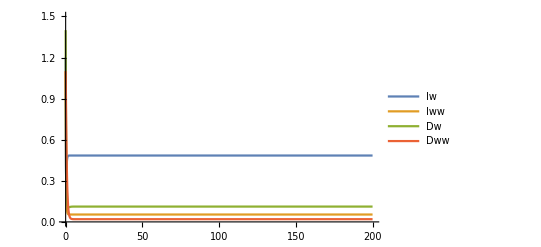

```mathematica
Plot[Evaluate[resvart/.nsolres1],{t, 0, tmax}, PlotRange->{{0, tmax} , {0, 1.5}}, PlotLegends->{"Iw", "Iww", "Dw", "Dww"}]
```